```mathematica
SetDirectory@NotebookDirectory[];
Import["QLanczos_package.m"];
```

## Parameters

```mathematica
κ=0.1;
η=1.5*10^-15;(*machine precision*)
ηList=Table[10.^j,{j,-13,-1,0.1}];
```

## Model

```mathematica
Ham=HeisenbergHam;
```

## Spectrum

```mathematica
{Λ,U}=funSpectrum[N[Ham]];
HamNorm=Max[Abs[Λ]];
Λ=Λ/HamNorm;
Eg=Λ[[1]]
```

-1.

```mathematica
htot=27./HamNorm
```

1.58524

## Reference state

```mathematica
φ=φHeisenberg;
φ=Flatten[Conjugate[U].φ];
probφ=Abs[φ]^2;
```

```mathematica
pg=probφ[[1]]
ER=Total[probφ*Λ];
ϵR=ER-Eg
```

0.682614

0.119312

## Power

```mathematica
dList={5,7,10,15,30};
MListP={};
ϵListP={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
{MList,ϵList}=funEpsilonM[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListP,MList];
AppendTo[ϵListP,ϵList];
,{i,1,Length[dList]}];
```

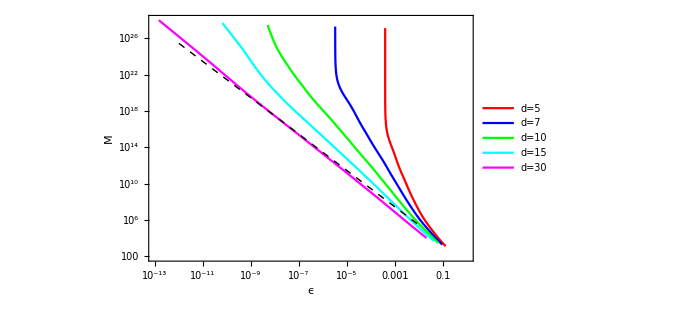

```mathematica
PR={{10.^-13,10.^0},{10.^2,10.^28}};
plotP=ListLogLogPlot[{Transpose[{ϵListP[[1]],MListP[[1]]}],Transpose[{ϵListP[[2]],MListP[[2]]}],Transpose[{ϵListP[[3]],MListP[[3]]}],Transpose[{ϵListP[[4]],MListP[[4]]}],Transpose[{ϵListP[[5]],MListP[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=15","d=30"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListP[[5]]],Log[MListP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListP[[5]]],Log[MListP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Chebyshev Polynomial

```mathematica
dList={5,7,10,15,30};
MListCP={};
ϵListCP={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=0;
{Hmat,Smat}=funMatCP[Λ,E0,d,probφ,htot];
{MList,ϵList}=funEpsilonM[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListCP,MList];
AppendTo[ϵListCP,ϵList];
,{i,1,Length[dList]}];
```

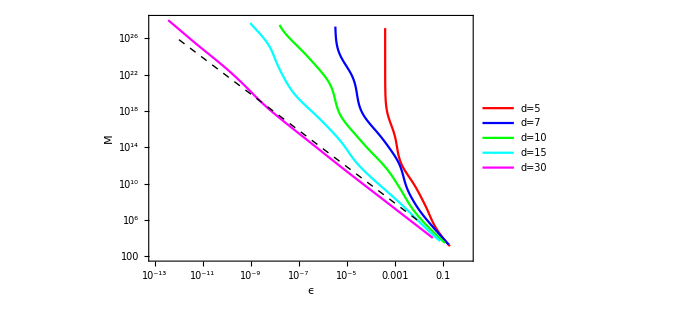

```mathematica
plotCP=ListLogLogPlot[{Transpose[{ϵListCP[[1]],MListCP[[1]]}],Transpose[{ϵListCP[[2]],MListCP[[2]]}],Transpose[{ϵListCP[[3]],MListCP[[3]]}],Transpose[{ϵListCP[[4]],MListCP[[4]]}],Transpose[{ϵListCP[[5]],MListCP[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=15","d=30"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListCP[[5]]],Log[MListCP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListCP[[5]]],Log[MListCP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Gaussian-Power

```mathematica
dList={2,3,4,5,6};
MListGP={};
ϵListGP={};

Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg;

τMIN=Sqrt[(d-1)/E];
τMAX=Sqrt[d-1]/0.1;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatGP[Λ,Eg,τ,1,probφ,htot];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;Print["τ_GP:",τ];

δ=RandomReal[{-0.1,0.1}];
E0=Eg+δ;
{Hmat,Smat}=funMatGP[Λ,E0,τ,d,probφ,htot];
{MList,ϵList}=funEpsilonM[Hmat,Smat,htot,1.,Id,ηList,Eg,d,κ];
AppendTo[MListGP,MList];
AppendTo[ϵListGP,ϵList];
,{i,1,Length[dList]}];
```

τ_GP:2.56034

τ_GP:3.9666

τ_GP:5.24256

τ_GP:6.34638

τ_GP:7.26576

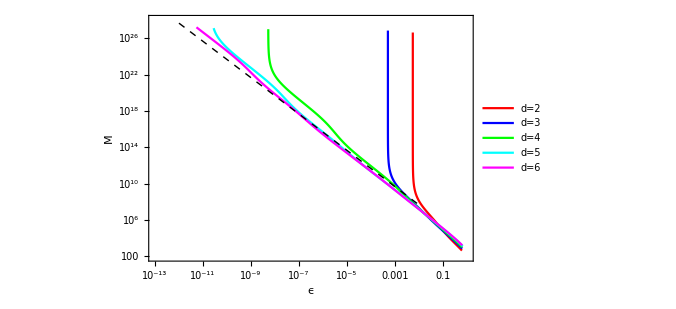

```mathematica
plotGP=ListLogLogPlot[{Transpose[{ϵListGP[[1]],MListGP[[1]]}],Transpose[{ϵListGP[[2]],MListGP[[2]]}],Transpose[{ϵListGP[[3]],MListGP[[3]]}],Transpose[{ϵListGP[[4]],MListGP[[4]]}],Transpose[{ϵListGP[[5]],MListGP[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=2","d=3","d=4","d=5","d=6"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListGP[[5]]],Log[MListGP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListGP[[5]]],Log[MListGP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Inverse Power

```mathematica
dList={5,7,10,15,30};
MListIP={};
ϵListIP={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=Eg-1.;
{Hmat,Smat}=funMatIP[Λ,E0,d,probφ];
{MList,ϵList}=funEpsilonM[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListIP,MList];
AppendTo[ϵListIP,ϵList];
,{i,1,Length[dList]}];
```

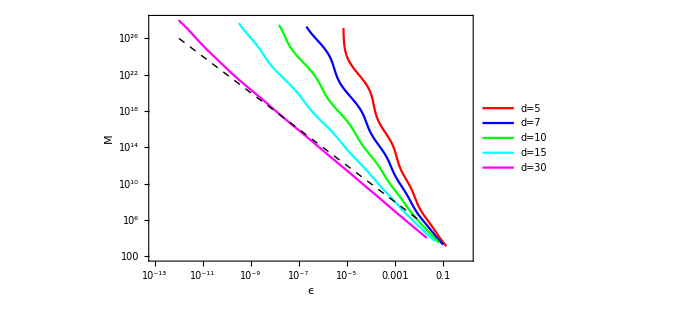

```mathematica
plotIP=ListLogLogPlot[{Transpose[{ϵListIP[[1]],MListIP[[1]]}],Transpose[{ϵListIP[[2]],MListIP[[2]]}],Transpose[{ϵListIP[[3]],MListIP[[3]]}],Transpose[{ϵListIP[[4]],MListIP[[4]]}],Transpose[{ϵListIP[[5]],MListIP[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=15","d=30"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListIP[[5]]],Log[MListIP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListIP[[5]]],Log[MListIP[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Imaginary-time Evolution

```mathematica
dList={5,7,10,15,30};
MListITE={};
ϵListITE={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg;

τMIN=0;
τMAX=128;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatITE[Λ,Eg,τ,d,probφ];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;Print["τ_ITE:",τ];
E0=Eg;
{Hmat,Smat}=funMatITE[Λ,E0,τ,d,probφ];
{MList,ϵList}=funEpsilonM[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListITE,MList];
AppendTo[ϵListITE,ϵList];
,{i,1,Length[dList]}];
```

τ_ITE:1.1768

τ_ITE:1.14179

τ_ITE:1.1235

τ_ITE:1.11794

τ_ITE:1.11733

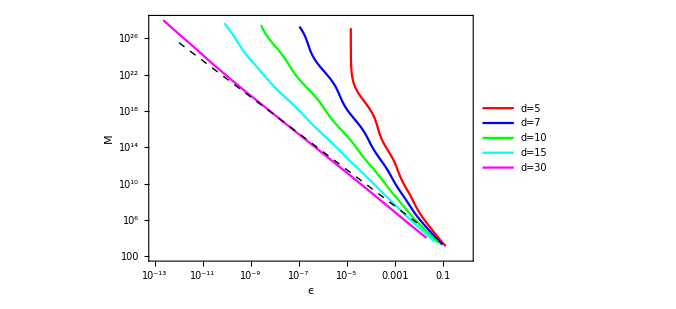

```mathematica
plotITE=ListLogLogPlot[{Transpose[{ϵListITE[[1]],MListITE[[1]]}],Transpose[{ϵListITE[[2]],MListITE[[2]]}],Transpose[{ϵListITE[[3]],MListITE[[3]]}],Transpose[{ϵListITE[[4]],MListITE[[4]]}],Transpose[{ϵListITE[[5]],MListITE[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=15","d=30"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListITE[[5]]],Log[MListITE[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListITE[[5]]],Log[MListITE[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Real-time Evolution

```mathematica
dList={5,7,10,15,30};
MListRTE={};
ϵListRTE={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

ΔtList=Table[((2.*π)/100)j,{j,1,100}];
ϵList=ConstantArray[0,Length[ΔtList]];
Do[
Δt=ΔtList[[j]];
{Hmat,Smat}=funMatRTE[Λ,Eg,Δt,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=Abs[EK-Eg];
ϵList[[j]]=err;
,{j,1,Length[ΔtList]}];
Δt=ΔtList[[Position[ϵList,Min[ϵList]][[1,1]]]];Print["Δt:",Δt];
E0=Eg;
{Hmat,Smat}=funMatRTE[Λ,E0,Δt,d,probφ];
{MList,ϵList}=funEpsilonMRTE[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListRTE,MList];
AppendTo[ϵListRTE,ϵList];
,{i,1,Length[dList]}];
```

Δt:0.314159

Δt:0.753982

Δt:1.3823

Δt:2.38761

Δt:5.65487

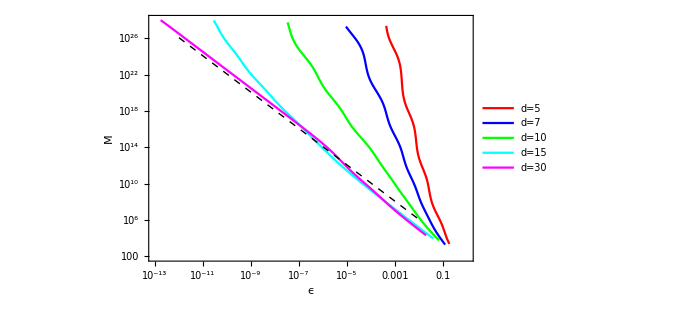

```mathematica
plotRTE=ListLogLogPlot[{Transpose[{ϵListRTE[[1]],MListRTE[[1]]}],Transpose[{ϵListRTE[[2]],MListIP[[2]]}],Transpose[{ϵListRTE[[3]],MListRTE[[3]]}],Transpose[{ϵListRTE[[4]],MListRTE[[4]]}],Transpose[{ϵListRTE[[5]],MListRTE[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=15","d=30"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListRTE[[5]]],Log[MListRTE[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListRTE[[5]]],Log[MListRTE[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

## Filter

```mathematica
dList={5,7,10,12,15};
MListF={};
ϵListF={};
Do[
d=dList[[i]];
Id=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg;

τMIN=0;
τMAX=1024;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatF[Λ,Eg,0,τ,1,probφ];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;Print["τ_F:",τ];
ΔEList=Table[(2./(d*100))*j,{j,1,100}];
ϵList=ConstantArray[0,Length[ΔEList]];
Do[(
ΔE=ΔEList[[j]];
{Hmat,Smat}=funMatF[Λ,Eg,ΔE,τ,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=EK-Eg;
ϵList[[j]]=err;
),{j,1,Length[ΔEList]}];
ΔE=ΔEList[[Position[ϵList,Min[ϵList]][[1,1]]]];Print["ΔE:",ΔE];
E0=Eg;
{Hmat,Smat}=funMatF[Λ,E0,ΔE,τ,d,probφ];
{MList,ϵList}=funEpsilonM[Hmat,Smat,1.,1.,Id,ηList,Eg,d,κ];
AppendTo[MListF,MList];
AppendTo[ϵListF,ϵList];
,{i,1,Length[dList]}];
```

τ_F:11.2447

ΔE:0.02

τ_F:13.7022

ΔE:0.0485714

τ_F:15.3563

ΔE:0.092

τ_F:30.9147

ΔE:0.055

τ_F:61.796

ΔE:0.032

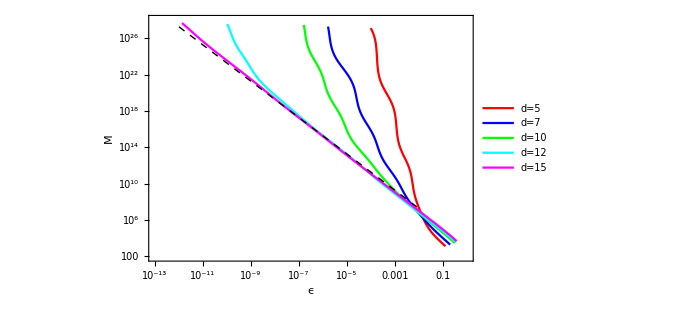

```mathematica
plotF=ListLogLogPlot[{Transpose[{ϵListF[[1]],MListF[[1]]}],Transpose[{ϵListF[[2]],MListF[[2]]}],Transpose[{ϵListF[[3]],MListF[[3]]}],Transpose[{ϵListF[[4]],MListF[[4]]}],Transpose[{ϵListF[[5]],MListF[[5]]}]},PlotStyle->{Red,Blue,Green,Cyan,Magenta},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Cyan},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"ϵ","M"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"d=5","d=7","d=10","d=12","d=15"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",1}],{0.1,0.25}],Epilog->{Dashed,Line[{{Log[10.^-12],Log[10.^24]+FindFit[Transpose[{Log[ϵListF[[5]]],Log[MListF[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]},{Log[10.^-2],Log[10.^4]+FindFit[Transpose[{Log[ϵListF[[5]]],Log[MListF[[5]]]}],-2*ϵ+b,{b},ϵ][[1,2]]}}]}]
```

```mathematica
path="scalingP.pdf";Export[path,plotP];
path="scalingCP.pdf";Export[path,plotCP];
path="scalingGP.pdf";Export[path,plotGP];
path="scalingIP.pdf";Export[path,plotIP];
path="scalingITE.pdf";Export[path,plotITE];
path="scalingRTE.pdf";Export[path,plotRTE];
path="scalingF.pdf";  Export[path,plotF];
```